Project 2
Nathan Solomon
UID: 905 746 764

```mathematica
(* 1 *)
Remove["Global`*"]
EquationList = {
	ξ == I1 R1 + I3 R3,
	ξ == I2 R2 + I4 R4,
	ξ == I1 R1 + I5 R5 + I4 R4,
	I1 == I5 + I3,
	I2 + I5 == I4
}
solution := Solve[EquationList, {I1, I2, I3, I4, I5}][[1]]
OverallResistance := ξ/(I1 + I2) /. solution
Print["Current through R5: ", Simplify[I5 /. solution]]
Print["Overall resistance of Wheatstone bridge: ", Simplify[OverallResistance]]
Print["If R1=R2 and R3=R4, then we expect that the current through R5 is zero, and the overall resistance is (R1 + R3)/2."]
Print["Current through R5: ", Simplify[I5 /. solution /. {R2->R1, R4->R3}]]
Print["Overall resistance of Wheatstone bridge: ", Simplify[OverallResistance /. {R2->R1, R4->R3}]]
```

{ξ==I1 R1+I3 R3,ξ==I2 R2+I4 R4,ξ==I1 R1+I4 R4+I5 R5,I1==I3+I5,I2+I5==I4}

Current through R5: ((R2 R3-R1 R4) ξ)/(R3 R4 R5+R1 R4 (R3+R5)+R2 R3 (R4+R5)+R1 R2 (R3+R4+R5))

Overall resistance of Wheatstone bridge: (R3 R4 R5+R1 R4 (R3+R5)+R2 R3 (R4+R5)+R1 R2 (R3+R4+R5))/((R3+R4) R5+R1 (R3+R4+R5)+R2 (R3+R4+R5))

If R1=R2 and R3=R4, then we expect that the current through R5 is zero, and the overall resistance is (R1 + R3)/2.

Current through R5: 0

Overall resistance of Wheatstone bridge: (R1+R3)/2

```mathematica
(* 2 *)
Remove["Global`*"]
r = {
	{R1, 0, R3, 0, 0},
	{0, R2, 0, R4, 0},
	{R1, 0, 0, R4, R5},
	{-1, 0, 1, 0, 1},
	{0, 1, 0, -1, 1}
};
i = {I1, I2, I3, I4, I5};
v = {ξ, ξ, ξ, 0, 0};
Print[r // MatrixForm, i // MatrixForm, " = ", v // MatrixForm]
Print[i // MatrixForm, " = ", MatrixForm[i = Simplify[Inverse[r] . v]]]
(* The following results all match the answers I got in problem one. This is good *)
Print["Current through R5: ", i[[5]]]
Print["Current through R5 when R1=R2 and R3=R4: ", Simplify[i[[5]] /. {R2->R1, R4->R3}]]
OverallResistance := ξ/(i[[1]]+i[[2]])
Print["Overall resistance of Wheatstone bridge: ", Simplify[OverallResistance]]
Print["Overall resistance of Wheatstone bridge when R1=R2 and R3=R4: ", Simplify[OverallResistance /. {R2->R1, R4->R3}]]
```

(R1 | 0 | R3 | 0 | 0
0 | R2 | 0 | R4 | 0
R1 | 0 | 0 | R4 | R5
-1 | 0 | 1 | 0 | 1
0 | 1 | 0 | -1 | 1)(I1
I2
I3
I4
I5) = (ξ
ξ
ξ
0
0)

(I1
I2
I3
I4
I5) = (((R4 R5+R2 (R3+R4+R5)) ξ)/(R3 R4 R5+R1 R4 (R3+R5)+R2 R3 (R4+R5)+R1 R2 (R3+R4+R5))
((R3 R5+R1 (R3+R4+R5)) ξ)/(R3 R4 R5+R1 R4 (R3+R5)+R2 R3 (R4+R5)+R1 R2 (R3+R4+R5))
((R1 R4+R4 R5+R2 (R4+R5)) ξ)/(R3 R4 R5+R1 R4 (R3+R5)+R2 R3 (R4+R5)+R1 R2 (R3+R4+R5))
((R3 (R2+R5)+R1 (R3+R5)) ξ)/(R3 R4 R5+R1 R4 (R3+R5)+R2 R3 (R4+R5)+R1 R2 (R3+R4+R5))
((R2 R3-R1 R4) ξ)/(R3 R4 R5+R1 R4 (R3+R5)+R2 R3 (R4+R5)+R1 R2 (R3+R4+R5)))

Current through R5: ((R2 R3-R1 R4) ξ)/(R3 R4 R5+R1 R4 (R3+R5)+R2 R3 (R4+R5)+R1 R2 (R3+R4+R5))

Current through R5 when R1=R2 and R3=R4: 0

Overall resistance of Wheatstone bridge: (R3 R4 R5+R1 R4 (R3+R5)+R2 R3 (R4+R5)+R1 R2 (R3+R4+R5))/((R3+R4) R5+R1 (R3+R4+R5)+R2 (R3+R4+R5))

Overall resistance of Wheatstone bridge when R1=R2 and R3=R4: (R1+R3)/2

x_1(t) = ((k Sin[t √(k (1/m_1+1/m_2))] m_1 m_2^2 (v_10-v_20))/(√(k m_1 m_2 (m_1+m_2)))+k m_1 (t v_10+x_10)+k m_2 (-L+t v_20+Cos[t √(k (1/m_1+1/m_2))] (L+x_10-x_20)+x_20))/(k (m_1+m_2))

x_2(t) = 1/(k (m_1+m_2)^2)(-Sin[t √(k (1/m_1+1/m_2))] √(k m_1^3 m_2 (m_1+m_2)) v_10+Sin[t √(k (1/m_1+1/m_2))] √(k m_1^3 m_2 (m_1+m_2)) v_20-k Cos[t √(k (1/m_1+1/m_2))] m_1 (m_1+m_2) (L+x_10-x_20)+k (m_1+m_2) (m_1 (L+t v_10+x_10)+m_2 (t v_20+x_20)))

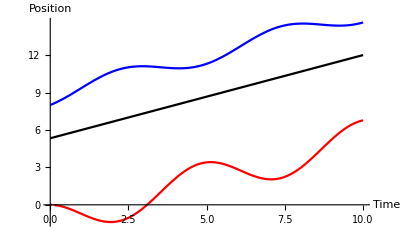

```mathematica
(* 3 *)
Remove["Global`*"]
$Assumptions = k>0 && L>0 && Subscript[m, 1]>0 && Subscript[m, 2]>0 && Element[{Subscript[x, 1][t], Subscript[x, 2][t]}, Reals];
equations = {
	k (Subscript[x, 2][t] - Subscript[x, 1][t] - L) == Subscript[m, 1] Subscript[x, 1]''[t],
	-k (Subscript[x, 2][t] - Subscript[x, 1][t] - L) == Subscript[m, 2] Subscript[x, 2]''[t],
	Subscript[x, 1][0] == Subscript[x, 10],
	Subscript[x, 2][0] == Subscript[x, 20],
	Subscript[x, 1]'[0] == Subscript[v, 10],
	Subscript[x, 2]'[0] == Subscript[v, 20]
};
solution = DSolve[equations, {Subscript[x, 1], Subscript[x, 2]}, t][[1]];
(* I compared answers with friends, and their answers look equivalent but different. Maybe the terms
alphabetize differently if you use subscripts (e.g. Subscript[x, 10] instead of x10) *)
Print["x_1(t) = ", FullSimplify[Subscript[x, 1][t] /. solution], "\n"]
Print["x_2(t) = ", FullSimplify[Subscript[x, 2][t] /. solution]]

solution = Join[solution, {Subscript[x, 10]->0, Subscript[x, 20]->8, Subscript[v, 10]->0, Subscript[v, 20]->1, k->5, L->10, Subscript[m, 1]->5, Subscript[m, 2]->10}];
Subscript[x, 1][t_] = Subscript[x, 1][t] /. solution;
Subscript[x, 2][t_] = Subscript[x, 2][t] /. solution;
CenterOfMass[t_] := (Subscript[m, 1] Subscript[x, 1][t] + Subscript[m, 2] Subscript[x, 2][t]) / (Subscript[m, 1] + Subscript[m, 2]) /. solution

plot1 := Plot[Subscript[x, 1][t] /. solution, {t, 0, 10}, PlotStyle->Red, PlotRange->All, AxesLabel->{"Time", "Position"}]
plot2 := Plot[Subscript[x, 2][t] /. solution, {t, 0, 10}, PlotStyle->Blue, PlotRange->All]
plot3 := Plot[CenterOfMass[t], {t, 0, 10}, PlotStyle->Black, PlotRange->All]
Show[plot1, plot2, plot3, PlotRange->All]
```

```mathematica
(* 4 *)
Remove["Global`*"]
(* Is there any way to do this without repeating nearly all the code from exercise 3??? *)
k = 5;
L = 10;
Subscript[m, 1] = 5;
Subscript[m, 2] = 10;
equations := {
	k (Subscript[x, 2][t] - Subscript[x, 1][t] - L) == Subscript[m, 1] Subscript[x, 1]''[t],
	-k (Subscript[x, 2][t] - Subscript[x, 1][t] - L) == Subscript[m, 2] Subscript[x, 2]''[t],
	Subscript[x, 1][0] == 0,
	Subscript[x, 2][0] == 8,
	Subscript[x, 1]'[0] == 0,
	Subscript[x, 2]'[0] == 1
};
solution = NDSolve[equations, {Subscript[x, 1], Subscript[x, 2]}, {t, 0, 10}][[1]];
Subscript[x, 1][t_] = Subscript[x, 1][t] /. solution;
Subscript[x, 2][t_] = Subscript[x, 2][t] /. solution;
CenterOfMass[t_] := (Subscript[m, 1] Subscript[x, 1][t] + Subscript[m, 2] Subscript[x, 2][t]) / (Subscript[m, 1] + Subscript[m, 2])

Animate[Show[
	Graphics3D[{
		Red, Cuboid[Sequence @@ ({{-1, -1, -1}, {1, 1, 1}} + {{1, 0, 0}, {1, 0, 0}} * Subscript[x, 1][t])],
		Blue, Cuboid[Sequence @@ ({{-1, -1, -1}, {1, 1, 1}} * 2^(1/3) + {{1, 0, 0}, {1, 0, 0}} * Subscript[x, 2][t])]
	}, Axes->True, Boxed->False, AxesOrigin->{0, 0, 0}],
	ParametricPlot3D[{Subscript[x, 1][τ], τ - t, 0}, {τ, 0, 10}, PlotStyle->Red],
	ParametricPlot3D[{Subscript[x, 2][τ], τ - t, 0}, {τ, 0, 10}, PlotStyle->Blue],
	ParametricPlot3D[{CenterOfMass[τ], τ - t, 0}, {τ, 0, 10}, PlotStyle->Black],
	(* Spring should start on faces of blocks, not their centers, hence the funny-looking math *)
	ParametricPlot3D[{(Subscript[x, 1][t] + 1) + s (Subscript[x, 2][t] - Subscript[x, 1][t] - (2^(1/3) - 1)), Cos[100 s], Sin[100 s]}, {s, 0, 1}, PlotStyle->Black],
	(* Draw invisible lines whose endpoints are included in the plot, forcing the x-axis to remain still *)
	ParametricPlot3D[{x, 0, 0}, {x, -5, 20}, PlotStyle->GrayLevel[0, 0]],
	ParametricPlot3D[{0, y, 0}, {y, -10, 10}, PlotStyle->GrayLevel[0, 0]]
], {t, 0, 10}, ControlPlacement->Top]
```